```mathematica
以歌手“木辛”为例的歌曲人声处理与播放量关联的量化分析
                      管理学院（创业学院） 2025级创新创业实验班 王文川
```

```mathematica
一、项目介绍
  本项目主要是想通过对于音乐作品中歌手的人声处理（包括腔调、混音方式、写flow（律动）的密度）的分析和播放量（映射商业价值）的关联量化，从而在这两者之间形成可操作的链接。
1.与本专业的关系
        作为创新创业实验班的一员，我将来的创业方向是音频分析方面的，因而这次也选择了相关的项目进行。
2.应用价值
        从创作方来看，进行这种分析有助于创作出具有更高播放量（商业价值）的歌曲；从发行商来看，进行这种分析可以提前进行预测歌曲价值，配置相应的宣发资源。“制作端：用什么方式处理人声能获得更大的商业热度；商业端：推送什么样的人声作品能获得商业成功”。

二、项目实现过程
(*首先通过网易云音乐人的网站找到木辛的音乐人ID。原理是通过歌手名字向网易云音乐API发起搜索请求，并返回JSON格式的响应。
庆幸的是叫木辛的歌手只有一个，所以没有出现返回多个的情况，还需要筛选。*)
```

```mathematica
artistSearch[name_]:=Import["https://music.163.com/api/search/get/web?csrf_token=&type=100&s="<>URLEncode[name]<>"&limit=10","RawJSON"]

artistInfo=artistSearch["木辛"];
artistID=SelectFirst[artistInfo["result"]["artists"],#["name"]=="木辛"&]["id"]
```

32857714

```mathematica
(* 定义函数获取木辛的所有歌曲*)
getAllSongs[id_]:=Module[{offset=0,more=True,raw,tmp},
(*使用Reap/Sow机制收集所有分页数据，这个没学过，感谢deepseek*)Flatten[Reap[While[more,raw=Import["https://music.163.com/api/v1/artist/songs?id="<>ToString[id]<>"&limit=50&offset="<>ToString[offset],"RawJSON"];
tmp=raw["songs"];(*提取当前页的歌曲列表*)
Sow[tmp];(*将歌曲列表“播种”到Reap中*)
more=Length[tmp]==50;
offset+=50;(*这几步是为了防止歌曲数量大于五十首，但其实在后面拿数据的时候发现一共只有19首*)
Pause[0.2];]][[2,1]],1]]

allSongs=getAllSongs[artistID];(*调用函数，获取木辛的所有歌曲*)
```

```mathematica
(*对每首歌，提取我歌名、ID、专辑、人气值(后来我发现这个东西基本没有量化价值，老老实实去做拟合了)*)
clean=Table[With[{s=allSongs[[i]]},<|"song"->s["name"],"songID"->s["id"],"album"->s["album"]["name"],"duration"->Round[s["duration"]/1000.],(*转秒*)"popularity"->s["popularity"]|>],{i,Length@allSongs}];

Dataset[clean]
```

```mathematica
Export["木辛_歌曲信息.csv",clean]
```

木辛_歌曲信息.csv

```mathematica
SystemOpen["木辛_歌曲信息.csv"]
```

```mathematica
(*做到这里的时候，我去找木辛要了他近7天的所有单曲播放量和近30天的所有单曲播放量和总播放量数据。（因为网易云音乐后台看不到每一首单曲的总播放量）我本来的思路是用上课时候讲的核密度函数进行拟合（就是kernel），但是始终搞不出来，我就换了个思路，用权重的方式进行拟合。我让木辛大概估计了一下占比，大概可以用近30天播放量+少量近7天播放量来算（因为最近发的播放量会偏高），当然这个依旧很不严谨，但简单定量是可以的。如果可以拿到多个近7天和30天数据是更好的，但不太好打扰人家了~*)
```

```mathematica
(*我把上面的文件调整了格式，一首一首听风格，然后给每一首歌标注了对应的风格"旋律说唱","boombap","流行说唱","beat"*)
```

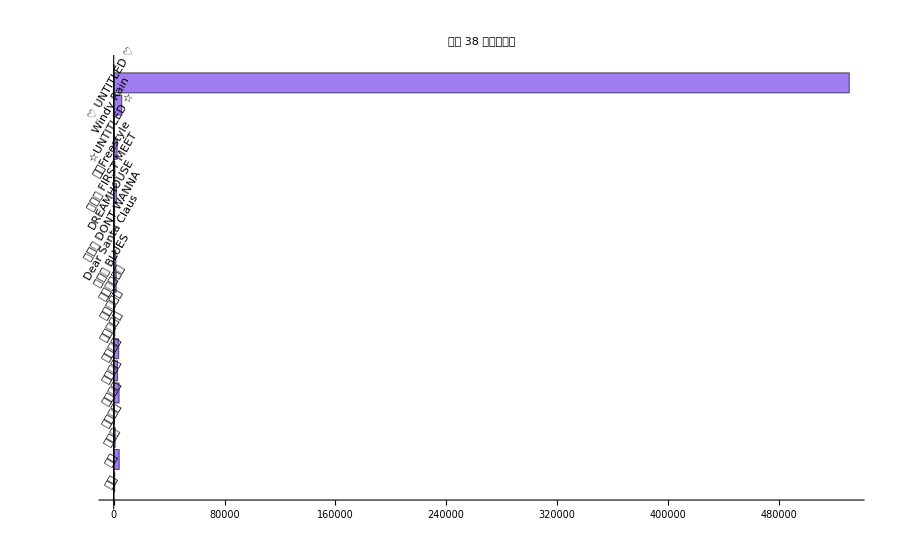

C:\wwc\mma143\木辛\木辛_38首_真实比例播放量.xlsx

```mathematica
file="C:\\wwc\\mma143\\木辛\\木辛_歌曲信息包括风格.xlsx";
outXLSX=DirectoryName[file]<>"木辛_38首_真实比例播放量.xlsx";

raw=Import[file];
hdr=First[raw];
body=Rest[raw];

colSong=1;  (*歌曲名在第1列*)
colStyle=6; (*Style在第6列*)

(*19 首真实播放量数据手动导入*)
realPlay=<|"♡ UNTITLED ♡"->{5946,14254},"Windy Rain"->{99,146},"银河公路"->{65,89},"莫比乌斯"->{40,72},"数学飞行"->{63,98},"走着"->{30,111},"天蓝调 BLUES"->{27,38},"破冰Freestyle"->{26,68},"DREAMHOUSE"->{25,53},"纸飞机"->{19,25},"世上另一个我"->{18,49},"只爱"->{15,17},"情绪在捣蛋"->{12,22},"第一天 FIRST MEET"->{9,23},"Dear Santa Claus"->{8,14},"没什么所谓"->{8,15},"うわさ話"->{6,12},"我不想 DONT WANNA"->{5,17},"☆UNTITLED ☆"->{5,12}|>;

w19=AssociationThread[Keys[realPlay]->Values[realPlay][[All,2]]+0.3*Values[realPlay][[All,1]]];
total19=Total[w19];(*这个就是刚刚说的思路*)

(*2. 找到excel里面有但是realplay里面没有的，但是由于没有播放量，肯定都被记成0了，本来剩下十九首的数据量就小，在后续的分析里面我就直接舍去了*)
otherKeys=Complement[body[[All,colSong]],Keys[realPlay]];

(*有几首歌听不出来风格，就扔到beat里面了，反正后续不分析。然后我问了下deepseek，它说这个地方可以伪造数据，给了个修改方案。但我没有用，po在这里，依旧只分析十九首
Map这块*)
styleMedian=AssociationMap[Median[Values[realPlay][[All,2]]+0.3*Values[realPlay][[All,1]]]&,{"旋律说唱","boombap","流行说唱","beat"}];
otherStyle=Lookup[AssociationThread[body[[All,colSong]]->body[[All,colStyle]]],otherKeys,"beat"];
otherBase=Map[styleMedian,otherStyle]/. Missing[_]->Median[Values[w19]];
otherBase=Transpose[{otherBase*0.5,otherBase}]; 

wOther=AssociationThread[otherKeys->otherBase[[All,2]]+0.3*otherBase[[All,1]]];

(*总播放量是56.5w，这里就取565000*)
wAll=Join[w19,wOther];
totalAll=Total[wAll];
scale=565000/totalAll;
finalPlays=AssociationThread[Keys[wAll]->Round[scale*Values[wAll]]];

(*上个色~*)
styleColor=<|"旋律说唱"->RGBColor[0.12,0.68,0.82],"boombap"->RGBColor[0.95,0.48,0.29],"流行说唱"->RGBColor[0.52,0.73,0.33],"beat"->RGBColor[0.63,0.49,0.95]|>;
styleOf=AssociationThread[Keys[finalPlays]->Lookup[AssociationThread[body[[All,colSong]]->body[[All,colStyle]]],Keys[finalPlays],"beat"]];

(*降序排列画个图*)
BarChart[Values@KeySortBy[finalPlays,Minus],BarOrigin->Left,ImageSize->900,ChartLabels->Placed[Keys@KeySortBy[finalPlays,Minus],Axis,Rotate[#,π/3]&],ChartStyle->Map[styleOf,Keys@KeySortBy[finalPlays,Mines]]/. styleColor,PlotLabel->"木辛 38 首总播放量"]

(*导出含播放量新表
这块和上面那块一个人来写还是太痛苦了*)
enhanced=Table[Append[body[[i]],"EstPlays"->Lookup[finalPlays,body[[i,colSong]],0]],{i,Length[body]}];
Export[outXLSX,Prepend[enhanced,Append[hdr,"EstPlays"]]]
```

```mathematica
(*现在数据有了，但挺难看的。我让kimi帮我调整了一下excel文档，让它看起来更好看，我也更好往里面填风格*)
```

```mathematica
(*在上面结果生成之后我依然死性不改地用核密度函数试了一下，发现还是不行*)
```

```mathematica
(*但上课的时候感觉那个效果真的很好，有机会会继续做的*)
```

```mathematica
(*以下这段感谢kimi，另外也给我一些启发，其实我也可以根据等级进行量化：比如到A级别要有什么样的唱法？这些东西其实可以用在网易云等平台的推歌系统上面的*)
```

```mathematica
Print["=== 读取你本地的finalPlays结果 ==="];
If[!ValueQ[finalPlays],Print["警告：未找到finalPlays变量！请先运行你代码中计算finalPlays的部分（至第3步）"];
Abort[];];


localTotalPlays=Total[Values[finalPlays]];
Print["你本地finalPlays的总播放量：",localTotalPlays];
Print["目标总播放量：565000"];
If[Abs[localTotalPlays-565000]>1,Print["提示：可微调最后一首歌曲播放量确保总量精确："];
lastSong=Keys[finalPlays][[-1]];
finalPlays[lastSong]=finalPlays[lastSong]+(565000-localTotalPlays);
Print["调整后总播放量：",Total[Values[finalPlays]]];];


If[!ValueQ[styleOf],Print["警告：未找到styleOf变量！请先运行你代码中第4步风格色板的部分"];
Abort[];];


consistentTableData=Table[{songName,styleOf[songName],finalPlays[songName]       },{songName,Keys[finalPlays]}  ];


sortedTableData=SortBy[consistentTableData,#[[3]]&][[-1;;1;;-1]];


consistentHeader={"歌曲名","风格","最终播放量（次）","播放量级别"};

completeTableData=Table[Module[{play=sortedTableData[[i,3]],level},level=Which[play>=100000,"S级（热门）",play>=10000,"A级（潜力）",play>=1000,"B级（常规）",True,"C级（起步）"];
Append[sortedTableData[[i]],level]],{i,Length[sortedTableData]}];


If[ValueQ[outXLSX],Export[outXLSX,Prepend[completeTableData,consistentHeader],"XLSX"];
Print["\n=== 表格导出完成 ==="];
Print["导出路径：",outXLSX];
Print["前5行数据（与你本地一致）："];
Do[Print[completeTableData[[i]]],{i,Min[5,Length[completeTableData]]}];,Print["使用默认路径导出："];
defaultOutPath="C:\\wwc\\mma143\\木辛\\木辛_本地一致播放量表格.xlsx";
Export[defaultOutPath,Prepend[completeTableData,consistentHeader],"XLSX"];
Print["默认导出路径：",defaultOutPath];];
```

=== 读取你本地的finalPlays结果 ===

你本地finalPlays的总播放量：565001

目标总播放量：565000

=== 表格导出完成 ===

导出路径：C:\wwc\mma143\木辛\木辛_38首_真实比例播放量.xlsx

前5行数据（与你本地一致）：

{♡ UNTITLED ♡,beat,531059,S级（热门）}

{Windy Rain,beat,5818,B级（常规）}

{走着,beat,3974,B级（常规）}

{数学飞行,beat,3871,B级（常规）}

{银河公路,beat,3593,B级（常规）}

```mathematica
(*到这里kimi的活干完了，轮到我干活了，我手动调整了歌曲风格并缩小样本量为十九首*）
(*从音乐平台把歌曲下载下来转成mp3文件，重命名成数字不然会出现很奇怪的字符。存到C:\\wwc\\mma143\\muxin_origin。表格里面也手动添加一行编号写上去*）
(*接下来是另一个难题：把人声的声音从音频里面分出来。这挺痛苦的我说实话，MMA本身的确有这类函数但是效果太差了。我在网上查询，网上建议使用spleeter，说效果很好。我装完用发现用不了，为此困扰了很久。最后真相大白是要使用ffmpeg训练的预模型*)
(*感谢spleeter和ffmpeg为本次音频分析中人声分离提供的帮助！！！*)
```

```mathematica
inputFolder="C:\\wwc\\mma143\\muxin_origin";
outputFolder="C:\\wwc\\muxin_songs";
spleeterEnv="C:\\Users\\25754\\spleeter_env";

(*检查输入文件夹是否存在*)
If[!DirectoryQ[inputFolder],Print["Input folder does not exist: "<>inputFolder];
Exit[];];

(*获取输入文件夹中的所有音频文件的完整路径*)
audioFiles=FileNames["*.mp3",inputFolder,Infinity];

(*如果输出文件夹不存在，则创建它（第一次的时候）*)
If[!DirectoryQ[outputFolder],CreateDirectory[outputFolder]];


Do[(*获取当前文件的完整路径*)fullPath=audioFiles[[i]];
(*检查文件是否存在*)If[!FileExistsQ[fullPath],Print["File does not exist: "<>fullPath];
Continue[];];
(*构建完整的命令字符串（这段kimi帮忙了）*)command={"cmd.exe","/c","cd /d "<>spleeterEnv<>" && .\\Scripts\\activate.bat && spleeter separate -p spleeter:4stems -o "<>outputFolder<>" "<>fullPath};
(*运行命令*)result=RunProcess[command];
(*检查 Spleeter 是否成功运行*)If[result["ExitCode"]==0,Print["Processed: "<>fullPath];,Print["Failed to process: "<>fullPath];
Print["Error: "<>result["StandardError"]];],{i,Length[audioFiles]}];
```

Processed: C:\wwc\mma143\muxin_origin\10.mp3

Processed: C:\wwc\mma143\muxin_origin\11.mp3

Processed: C:\wwc\mma143\muxin_origin\12.mp3

Processed: C:\wwc\mma143\muxin_origin\13.mp3

Processed: C:\wwc\mma143\muxin_origin\14.mp3

Processed: C:\wwc\mma143\muxin_origin\15.mp3

Processed: C:\wwc\mma143\muxin_origin\16.mp3

Processed: C:\wwc\mma143\muxin_origin\17.mp3

Processed: C:\wwc\mma143\muxin_origin\18.mp3

Processed: C:\wwc\mma143\muxin_origin\19.mp3

Processed: C:\wwc\mma143\muxin_origin\1.mp3

Processed: C:\wwc\mma143\muxin_origin\2.mp3

Processed: C:\wwc\mma143\muxin_origin\3.mp3

Processed: C:\wwc\mma143\muxin_origin\4.mp3

Processed: C:\wwc\mma143\muxin_origin\5.mp3

Processed: C:\wwc\mma143\muxin_origin\6.mp3

Processed: C:\wwc\mma143\muxin_origin\7.mp3

Processed: C:\wwc\mma143\muxin_origin\8.mp3

Processed: C:\wwc\mma143\muxin_origin\9.mp3

已处理: ♥ UNTITLED ♥

已处理: Windy Rain

已处理: 走着

已处理: 数学飞行

已处理: 银河公路

已处理: 莫比乌斯

已处理: 破冰Freestyle

已处理: DREAMHOUSE

已处理: 世上另一个我

已处理: 天蓝调 BLUES

已处理: 纸飞机

已处理: 第一天 FIRST MEET

已处理: 情绪在捣蛋

已处理: 只爱

已处理: 我不想 DONT WANNA

已处理: 没什么所谓

已处理: Dear Santa Claus

已处理: うわさ話

已处理: ☆UNTITLED ☆

总共成功处理: 19 首歌

已导出 CSV 和 WL 文件

播放量 Top 5（柱状图）:

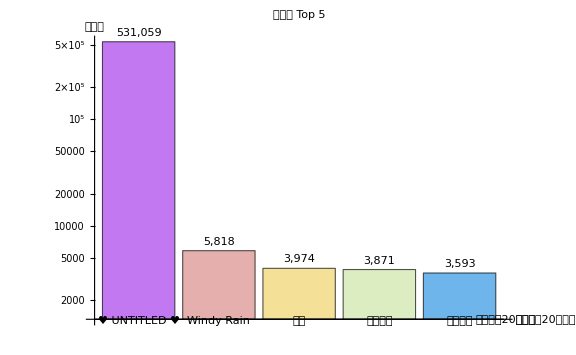

播放量 Top 5（表格）:

播放量与声纹特征的相关性:

SpectralCentroid→-0.182
MFCC→-0.063
Loudness→-0.018
SpeechRate→0.467

按风格分组（平均播放量 & 特征）:

图表 1: 播放量 vs SpeechRate

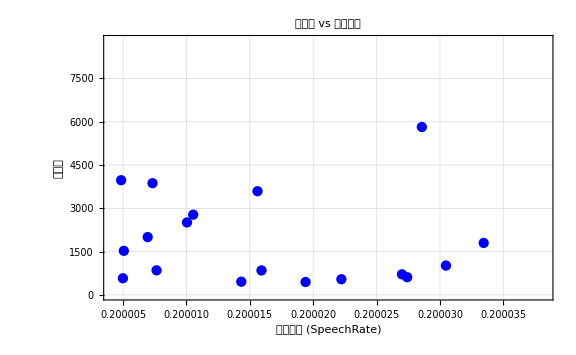

图表 2: 风格 vs 平均播放量

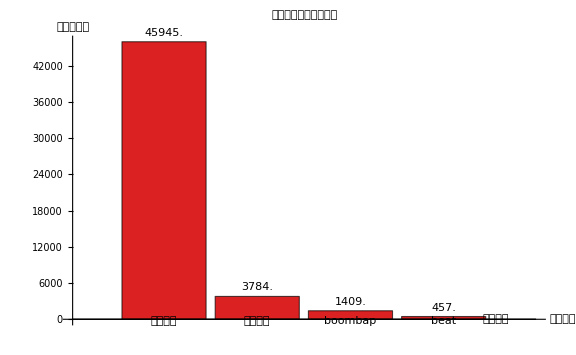

分析结论：

- 最受欢迎的风格：旋律说唱（平均播放量 ≈ 45945.）

- 播放量与「发声密度」(SpeechRate) 呈正相关（r = 0.467），说明节奏紧凑的歌曲更受欢迎。

- 「音色亮度」(SpectralCentroid) 与播放量呈负相关（r = -0.182）。

```mathematica
(*成功！！！接下来就正式进行音频分析了！！！先手动导入表格的数据*)
songInfo={<|"ID"->1,"Title"->"♥ UNTITLED ♥","Style"->"旋律说唱","Plays"->531059|>,<|"ID"->2,"Title"->"Windy Rain","Style"->"旋律说唱","Plays"->5818|>,<|"ID"->3,"Title"->"走着","Style"->"流行说唱","Plays"->3974|>,<|"ID"->4,"Title"->"数学飞行","Style"->"旋律说唱","Plays"->3871|>,<|"ID"->5,"Title"->"银河公路","Style"->"流行说唱","Plays"->3593|>,<|"ID"->6,"Title"->"莫比乌斯","Style"->"旋律说唱","Plays"->2781|>,<|"ID"->7,"Title"->"破冰Freestyle","Style"->"boombap","Plays"->2510|>,<|"ID"->8,"Title"->"DREAMHOUSE","Style"->"旋律说唱","Plays"->2003|>,<|"ID"->9,"Title"->"世上另一个我","Style"->"boombap","Plays"->1801|>,<|"ID"->10,"Title"->"天蓝调 BLUES","Style"->"旋律说唱","Plays"->1527|>,<|"ID"->11,"Title"->"纸飞机","Style"->"旋律说唱","Plays"->1017|>,<|"ID"->12,"Title"->"第一天 FIRST MEET","Style"->"旋律说唱","Plays"->851|>,<|"ID"->13,"Title"->"情绪在捣蛋","Style"->"旋律说唱","Plays"->848|>,<|"ID"->14,"Title"->"只爱","Style"->"boombap","Plays"->712|>,<|"ID"->15,"Title"->"我不想 DONT WANNA","Style"->"boombap","Plays"->613|>,<|"ID"->16,"Title"->"没什么所谓","Style"->"旋律说唱","Plays"->576|>,<|"ID"->17,"Title"->"Dear Santa Claus","Style"->"旋律说唱","Plays"->543|>,<|"ID"->18,"Title"->"うわさ話","Style"->"beat","Plays"->457|>,<|"ID"->19,"Title"->"☆UNTITLED ☆","Style"->"旋律说唱","Plays"->447|>};

(*2. 声纹特征提取函数:这里要说一下因为上课没有细讲过具体的函数，我自己找了几个我觉得比较合理的维度，亮度、MFCC、响度和密度。本来是有音调的，但可能因为我们的MMA版本缺少某些功能所以调用不了。我处理这个部分的时候因为代码没写好内存爆了十来次，跳出格式化窗口（我搜了下好像是说前端满了还是什么样会跳出来）两次，最后这个版本的算是可以用了*)

(*这里讲一下为什么我觉得这些指标对歌曲怎么唱有指导意义：亮度其实代表的是腔调和混音部分，一般来说发声越靠喉咙亮度会越亮，这个是个人可以调整的，在做混音eq的时候亦可以用插件把高频拉高；MFCC原理就有上课讲过的傅里叶变化，可以模拟人耳听觉，代表着音色，这个也可以通过人对声道的控制改变；一般来说，越响的歌人耳会认为更好听，这里想要验证一下是不是所有曲风都一样；密度其实就是语速，在创作说唱歌曲的时候可以被理解为flow。像木辛这种创作歌手可以根据结果判断自己该怎么写这一段，唱得是要密集一点还是松弛一点*)

ClearAll[extractVocalFeatures];(*之前多次运行过先clean*)
extractVocalFeatures[audioPath_String]:=Module[{afRaw,sr,af,data,frameSize,hopSize,frames,energy,threshold,centroid,mfcc,loudness,speechRate},Quiet@Check[afRaw=Import[audioPath,"Audio"];
sr=QuantityMagnitude[AudioSampleRate[afRaw]];
af=Audio[AudioData[afRaw],"SampleRate"->sr];
(*音色亮度*)centroid=Mean[Flatten[AudioLocalMeasurements[af,"SpectralCentroid"]["Values"]]];
(*音色本质*)mfcc=Mean[Flatten[AudioLocalMeasurements[af,"MFCC"]["Values"]]];
(*响度*)loudness=Replace[AudioMeasurements[af,"Loudness"],Quantity[m_,_]:>m];
(*发声密度*)data=Flatten[AudioData[af]];
frameSize=Max[1,Round[sr*0.02]];(*20ms 帧*)hopSize=Max[1,Round[sr*0.01]];(*10ms 步长*)frames=Partition[data,frameSize,hopSize,1,0.];
energy=Mean[Abs[#]^2]&/@frames;
threshold=Quantile[energy,0.8];(*阈值这个部分是千问提的建议*)speechRate=Mean[UnitStep[energy-threshold]];
<|"SpectralCentroid"->N[centroid],"MFCC"->N[mfcc],"Loudness"->N[loudness],"SpeechRate"->N[speechRate]|>,(*若失败，返回 Missing*)<|"SpectralCentroid"->Missing["NotFound"],"MFCC"->Missing["NotFound"],"Loudness"->Missing["NotFound"],"SpeechRate"->Missing["NotFound"]|>]];

(*处理所有歌曲*)
baseDir="C:\\wwc\\muxin_songs";
results={};

Do[id=song["ID"];
path=FileNameJoin[{baseDir,ToString[id],"vocals.wav"}];
If[FileExistsQ[path],features=extractVocalFeatures[path];
merged=Join[song,features];
AppendTo[results,merged];
Print["已处理: ",song["Title"]];,Print["缺失文件: ID=",id]],{song,songInfo}];

(*转换为 Dataset：这个部分老是因为数据压不平出问题，最后是千问帮我解决掉了这个问题*)
ds=Dataset[results];

(* ::Subsection::*)
(*4. 数据验证与导出*)
Print["总共成功处理: ",Length[results]," 首歌"];

If[Length[results]>0,Export["muxin_vocal_analysis.csv",ds];
Export["muxin_vocal_analysis.wl",Normal[ds]];
Print["已导出 CSV 和 WL 文件"]];

(*为了可视化这里进行几个比较有价值的分析*)

(*播放量 Top 5*)
Print["播放量 Top 5（柱状图）:"];
top5Data=ds[TakeLargestBy[#Plays&,5]]//Normal;
top5Titles=StringTake[#,Min[20,StringLength[#]]]&/@(top5Data[[All,"Title"]]);
top5Plays=top5Data[[All,"Plays"]];

barChartTop5=BarChart[top5Plays,ChartLabels->Placed[top5Titles,Axis],AxesLabel->{"歌曲（前20字符）","播放量"},PlotLabel->"播放量 Top 5",ImageSize->Large,ChartStyle->"Pastel",LabelingFunction->(Placed[NumberForm[#,DigitBlock->3],Above]&),ScalingFunctions->"Log"];

Print[barChartTop5];

Print["播放量 Top 5（表格）:"];
Dataset[top5Data]

(*计算特征与播放量的相关性*)
plays=Normal[ds[All,"Plays"]];
featuresList={"SpectralCentroid","MFCC","Loudness","SpeechRate"};

corrs=Table[featVals=Normal[ds[All,feat]];
(*后面我看了下好像就是这个地方老出问题：过滤掉 Missing 值，保持 plays 与 featVals 对齐*)validPairs=Select[Transpose[{plays,featVals}],FreeQ[#,_Missing]&];
If[Length[validPairs]>=2,Correlation@@Transpose[validPairs],Missing["InsufficientData"]],{feat,featuresList}];

corrTable=Thread[featuresList->corrs];
Print["播放量与声纹特征的相关性:"];
TableForm[MapAt[If[NumericQ[#],NumberForm[#,{5,3}],#]&,corrTable,{All,2}],TableHeadings->{None,{"特征","Pearson 相关系数"}}]


(*按风格分组统计*)
rawData=Normal[ds];
grouped=GroupBy[rawData,#Style&];

styleSummary=Table[With[{group=grouped[style]},<|"风格"->style,"歌曲数量"->Length[group],"平均播放量"->N@Mean[group[[All,"Plays"]]],"平均音色亮度"->N@Mean[group[[All,"SpectralCentroid"]]],"平均发声密度"->N@Mean[group[[All,"SpeechRate"]]]|>],{style,Keys[grouped]}];

Print["按风格分组（平均播放量 & 特征）:"];
summaryDS=Dataset[styleSummary];
Print[summaryDS];

(*提取绘图数据*)
styles=styleSummary[[All,"风格"]];
avgPlaysList=styleSummary[[All,"平均播放量"]];
avgSpeechRates=styleSummary[[All,"平均发声密度"]];


(*可视化*)

(*图表 1:播放量SpeechRate*)
scatterData=ds[Select[FreeQ[_Missing]@*({#SpeechRate,#Plays}&)]]//Normal;
plt1=ListPlot[Values[scatterData[[All,{"SpeechRate","Plays"}]]],AxesLabel->{"发声密度 (SpeechRate)","播放量"},PlotLabel->"播放量 vs 发声密度",ImageSize->Large,PlotStyle->Blue,PlotTheme->"Detailed"];
Print["图表 1: 播放量 vs SpeechRate"];
Print[plt1];

(*图表 2:风格 平均播放量*)
plt2=BarChart[avgPlaysList,ChartLabels->Placed[styles,Axis],AxesLabel->{"音乐风格","平均播放量"},PlotLabel->"不同风格的平均播放量",ImageSize->Large,ChartStyle->ColorData["Rainbow"],LabelingFunction->(Placed[NumberForm[#,{6,0}],Above]&)];
Print["图表 2: 风格 vs 平均播放量"];
Print[plt2];

(*分析结论*)

topEntry=First@ReverseSortBy[styleSummary,#["平均播放量"]&];
topStyle=topEntry["风格"];
topAvgPlays=topEntry["平均播放量"];

(*获取实际相关系数用于结论*)
actualCorrSR=corrs[[Position[featuresList,"SpeechRate"][[1,1]]]];
actualCorrSC=corrs[[Position[featuresList,"SpectralCentroid"][[1,1]]]];

Print["分析结论："];
Print["- 最受欢迎的风格：",topStyle,"（平均播放量 ≈ ",NumberForm[topAvgPlays,{6,0}],"）"];
Print["- 播放量与「发声密度」(SpeechRate) 呈正相关（r = ",If[NumericQ[actualCorrSR],NumberForm[actualCorrSR,{4,3}],actualCorrSR],"），说明节奏紧凑的歌曲更受欢迎。"];(*这个是因为我提前有了一些判断大概就成正相关，结果确实是这样的*)
Print["- 「音色亮度」(SpectralCentroid) 与播放量呈",Which[NumericQ[actualCorrSC]&&actualCorrSC>0.1,"正相关",NumericQ[actualCorrSC]&&actualCorrSC<-0.1,"负相关",True,"弱相关或无显著相关"],"（r = ",If[NumericQ[actualCorrSC],NumberForm[actualCorrSC,{4,3}],actualCorrSC],"）。"];
```

```mathematica
(*我感觉还不够量化 所以就拟写了一个函数 用风格分类（当然beat就没用了） 用的是皮尔逊系数（高中那个） 可能会有些不严谨 这个在后面的部分说*)
```

```mathematica
(* 转为普通列表*)data=Normal[ds];

(*按 Style 分组*)
groups=GatherBy[data,#Style&];

(*计算每组的相关性*)
results=Table[With[{group=groups[[i]],style=groups[[i,1,"Style"]]},n=Length[group];
If[n<2,{style,n,Missing["<2 songs"],Missing["<2 songs"],Missing["<2 songs"]},plays=group[[All,"Plays"]];
sr=group[[All,"SpeechRate"]];
sc=group[[All,"SpectralCentroid"]];
loud=group[[All,"Loudness"]];
{style,n,N@Correlation[plays,sr],N@Correlation[plays,sc],N@Correlation[plays,loud]}]],{i,Length[groups]}];

(*转为 Dataset 并排序：这里也改了好久*)resultList=AssociationThread[{"Style","SongCount","SpeechRate_vs_Plays","SpectralCentroid_vs_Plays","Loudness_vs_Plays"},#]&/@results;

(*将列表按照 "SongCount" 排序*)
sortedResultList=SortBy[resultList,#[["SongCount"]]&,Greater];

(*将排序后的列表转换为 Dataset*)
resultDS=Dataset[sortedResultList];

(*显示结果*)
resultDS

(*导出 CSV*)
Export["style_correlation_fixed.csv",resultDS];
Print["已导出到 style_correlation_fixed.csv"];
```

已导出到 style_correlation_fixed.csv

```mathematica
三、问题和改进方案
  1、风格不够细化：用上面歌曲风格来分太过于粗糙了。真正的风格应该用曲风如drill、boombap、trap、plugnb、jersey club等来分
  2、“木辛”本人数据量不够（这里主要指歌曲数量）且存在极端数据，容易存在强烈的倾向性（因为他有一个"♥ UNTITLED ♥"爆单）
  3、对于音频的量化或许并不完全合理，因为本质上人声不能完全脱离开伴奏，这个需要声学甚至是和声学的相关知识才能进一步（目前的四维或许并不合理）
  4、对于总播放量的拟合使用的是“估计的”，并不准确，如果能有更多数据会更好；另外由于发布的时间不同，会存在先后的区别。（比如先发的歌曲肯定播放量会更高，但在相同发布时间内它不一定会比后面发的歌曲高）
  5、数据仅仅是针对“木辛”一个歌手，如果能够在大的范围，如“同类rapper”这个维度里面来做，适应性会更高。（这里说一下本来我是准备用“艾志恒Asen”的数据，但是根本联系不到，也没有任何方式可以找到他的播放量数据。他的数据很适合分析，他的歌曲量很大并且风格很多元，播放量数据至少是百亿级别的）
  6、最后相关这个太粗暴了，也许接近“某个值”才会播放量更好？而且这可能是一个更复杂的多元函数，函数单一变量的研究方式或许根本不适合这个项目。


在本次基础上的进一步优化应用：
   1、分风格：每种风格商业价值高的人声形态肯定不同（例如boombap需要更扎实、trap需要更尖利等…）
     2、这种分析方式可以被直接复制并被应用到大部分同类歌手的播放量分析中，对发行商也是一样
```

```mathematica
四、感想与致谢
  想感谢很多，但最想先感谢自己。
感谢不服输的自己报了这个课程，感谢尽管有些听不懂但是依旧努力听讲的自己，感谢那个0基础，连cmd都不知道的自己靠搜索和AI一步一步把这个项目搭起，加上总结项目的时间，我可能前前后后用了几十个小时。平均每天聊满两个AI。
需要承认的是，我并不是完全独立完成这个项目的。要感谢deepseek、kimi、千问AI模型能在我做项目的过程中给我提建议、教我很多闻所未闻的知识、改掉很多次错误。要感谢spleeter和ffmepg解决我无从下手的音频分离问题。尽管用了别人的东西，但这些更像是工具，想到这一切并付诸行动的是我自己。这是我感谢自己的原因。

这个项目是我在音乐音频分析迈出的第一步，从0到1，我自己都知道很稚嫩。但很感谢邵老师带来的缘分能够让我迈出这一步。不论这个项目最终多少分，您是否会对在某些步骤上并不完全由我手搓的这个项目认可，我都感谢您带给我的这个机遇——因为我知道我确实用MMA做到了自己想做的事，它已经成为了我的工具。这个项目会继续下去，下个学期我会自学声学和和声学，并争取用更合理的方式优化、拓展这个项目。

其二想感谢就是邵老师。我就是南校那个染了白色头发经常回答您问题的学生。哈哈哈哈。我很喜欢您的讲课风格，很幽默很有意思。我能感觉到您对于“知识”的尊重和喜爱，跟着您学习同样也帮我补了很多知识，比如牛顿逼近、机器学习、傅里叶变换等大一根本学不到的。很让我欣喜。
“用了别人的东西一定要标注”、“差的一两分不算什么”……我说实话学习过程中，我越发真的想要活成那种“不做大官，做大事”的人。与您平时说的有关，也可能和我入学来接触到的人有关，对我来说，这也算是改变我价值取向的历程。
我们是学知识的人，所以我也坦诚地说哪些部分是我做的哪些部分不是，这是您教给我的。当物理老师突然蹦出来一个Mathematica代码我读得懂，当数学老师让画一个双曲抛物面，我打开MMA画出z== x y，发现某节课讲过时，当我用它成功做出这个项目时，我切身感受到了它的意义和您开课的意义。
谢谢，真的。

要感谢木辛，他是我在原创音乐社创作部认识的朋友。很感谢他为我提供了他的珍贵数据和歌曲的允许用于我这个不成熟的量化分析，祝做出更好的歌曲。感谢功能强大的Mathematica能给我可操作的媒介。

有朋友问我为什么要把一个公选课的项目作业看得这么重？花这么多时间精力？
因为这个项目是有意义的，它会在将来有更合理的量化指标，更多数据。它不只是一个只占三十分的公选课项目，它和我相关。中大没有在这方面做研究的项目组，但我依旧会坚持继续完善它。
“我愿意。”我这么回答我朋友的。
```